Correcting Non-Syntax Expression

Krotkikh Andrey

Roy Xavier

Perm National Research Polytechnical University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Find ways for correcting non-SyntaxQ expressions to SyntaxQ expressions.

SUMMARY OF WORK: We start with a Wolfram Language expression given as a string, which we evaluate using the symbol ToExpression. If $Failed is returned, it means that our string has not a correct syntax. To investigate possible ways of correcting an expression, we tried constructing a text analysing parser based on string patterns. We understood after benchmarking this method that it was a very inefficient approach. We therefore built instead a counting method (how many open and closed brackets, braces, etc., the string contains) and looked at a way of using errors issued by incorrect expressions when evaluated. We designed from this second approach an algorithm that convert non-SyntaxQ expressions to SyntaxQ expressions by adding one missing character. For any non-SyntaxQ expression, we were then able to generate (possibly several) SyntaxQ expressions. At the end of our work, we decided to construct a neural net in order to rank these corrections. We generated a dataset of pairs of non-SyntaxQ and SyntaxQ expressions from examples taken from the reference pages of about 2000 built-in symbols. This neural net is only a prototype and was not trained due to lack of time.

RESULTS AND FUTURE  WORK: Our main result has been the design of an algorithm that corrects non-SyntaxQ expressions to SyntaxQ expressions, and the prototype of neural net architecture to rank the corrected expressions. In future, we plan to construct a larger dataset to train our prototype. We will also improve the algorithm for supporting 2 or more missing characters.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Correct expressions with missing closing characters:

```mathematica
syntaxCorrector["{a,b"]
```

Closing brace missing
{a,b}

```mathematica
syntaxCorrector["f[1,2"]
```

Closing bracket missing
f[1,2]

Correct expressions with missing opening characters:

```mathematica
syntaxCorrector["f[x[],1,2}]"]
```

Opening brace missing
f[{x[],1,2}]
f[x[],{1,2}]
f[x[],1,{2}]
f[x[],1,2{}]

The solutions that are proposed take into account the number of arguments for built-in symbols:

```mathematica
syntaxCorrector["N@Nest[Nest[x^2,x,6,4,3]"]
```

Closing bracket missing
N@Nest[Nest[x^2,x,6],4,3]

We can specify options:

```mathematica
syntaxCorrector["Insert[{a,b,c,d,e},,2]"]
```

Letter or number Missed
Insert[{a,b,c,d,e},□,2]

```mathematica
syntaxCorrector["Insert[{a,b,c,d,e},,2]","NullChecking"->False]
```

All correct!

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]","NullChecking"->True]
```

Closing bracket missing
Fold[f[][],x[],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]","NullChecking"->False,FontSize->20,FontColor->Magenta]
```

Closing bracket missing
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]

We have a panel version that checks on the fly the input expressions:

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

1) We designed an algorithm that corrects Wolfram Language non-SyntaxQ expressions. This algorithm is shown below.
2) We investigated a first approach: using of string patterns
3) We tried to optimize all possible cases.
4) We found that the approach was very inefficient.
5) We investigated a second way: counting relevant characters of the string and analysing of error issues during evaluations.
6) We built the algorithm based on this approach.
7) We investigated the structure of neural net and possible datasets for training it.

Code

Provide one of:

Collapsed code

```mathematica
$SystemSymbols=Names["System`*"];
```

```mathematica
Clear[syntaxCorrector]
Options[syntaxCorrector]:={nullT->True,sizeT->16}
```

```mathematica
syntaxCorrector[str_String,opts:OptionsPattern[]]:=
Module[
{inp=str,
counts,
result={},
openbrack,
closebrack,
openbrace,
closebrace,
openparen,
closeparen},
{nulltest,size}=OptionValue[syntaxCorrector,{opts},{nullT,sizeT}];
counts=CharacterCounts[str];
openbrack=Lookup[counts,"[",0];
closebrack=Lookup[counts,"]",0];
openbrace=Lookup[counts,"{",0];
closebrace=Lookup[counts,"}",0];
openparen=Lookup[counts,"(",0];
closeparen=Lookup[counts,")",0];
If[messageAnalysis[str]&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest]),AppendTo[result,"All correct!"],
Which[
Not[openbrack==closebrack],
If[
openbrack>closebrack,
If[
openbrack-closebrack>1,
AppendTo[result,"Closing brackets missing"],
AppendTo[result,"Closing bracket missing"]
];
evaluation[str,nulltest,size,result,"]"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"]"]}]];
,
If[
-openbrack+closebrack>1,
AppendTo[result,"Opening brackets missing"],
AppendTo[result,"Opening bracket missing"]
];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"["]}]];
];
,
Not[StringCount[str,{"{"}]==StringCount[str,{"}"}]],
If[
openbrace>closebrace,
If[
openbrace-closebrace>1,
AppendTo[result,"Closing braces missing"],
AppendTo[result,"Closing brace missing"]
];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"}"]}]];
,
If[
-openbrace+closebrace>1,
AppendTo[result,"Opening braces missing"],
AppendTo[result,"Opening brace missing"]
];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"{"]}]];
];
,
Not[StringCount[str,{"("}]==StringCount[str,{")"}]],
If[
openparen>closeparen,
If[
openparen-closeparen>1,
AppendTo[result,"Closing parentheses missing"],
AppendTo[result,"Closing parenthes missing"]
];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,")"]}]];
,
If[
-openparen+closeparen>1,
AppendTo[result,"Opening parentheses missing"],
AppendTo[result,"Opening parenthes missing"]
];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"("]}]];
];
,
Not[EvenQ[StringCount[str,"\""]]],
AppendTo[result,"Quotes missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"\""]}]];
,
StringCount[str,{"["}]==StringCount[str,{"]"}]&&
StringCount[str,{"{"}]==StringCount[str,{"}"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
EvenQ[StringCount[str,"\""]],
AppendTo[result,"Letter or number Missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"□"]}]];
];
];
TableForm[Flatten[result]]
]
```

```mathematica
messageAnalysis[str_]:=
Module[{mess,result},
Block[{$MessageList={}},
Quiet[
ToExpression[str];
mess=$MessageList;
];
If[mess=!={},result=False,result=True];
(*
result = If[mess =!= {}, False, True];
result = (mess === {});
*)
];
result
];
```

```mathematica
testAnalyser[str_String,initStr_,nulltest_]:=messageAnalysis[str]&&EditDistance[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],initStr]>=1&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest])
```

```mathematica
Clear[stylingResult]
```

```mathematica
stylingResult[list_,symbol_String,size_Integer]:=
Module[
{l=list,s=symbol,ss=size,result,i},
result={};
For[i=1,i≤Length[l],i++,
AppendTo[
result,
TextCell[
Row[
{
StringTake[l⟦i,2⟧,{1,l⟦i,1⟧-1}],
Style[s,Red,FontSize->ss,Bold],
StringTake[l⟦i,2⟧,{l⟦i,1⟧+1,StringLength[l⟦i,2⟧]}]
}
]
]
]
];
result
]
```

```mathematica
correctSplitting[str_String]:=
Module[{s=str,s1,s2,result={},i},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[$SystemSymbols,s1[[i]]]],
s2=StringDrop[s1[[i]],{#}]&/@Range[StringLength[s1[[i]]]];
AppendTo[result,{s1[[1;;i-1]],s2[[#]],s1[[i+1;;]]}&/@Range[StringLength[s1[[i]]]]]
]
];
StringJoin/@Flatten[result,1]
]
```

```mathematica
Clear[correctInserting]
```

```mathematica
correctInserting[str_String,strinst_String]:=
Module[{s=str,s1,s2,result={},i,symb=strinst},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[$SystemSymbols,s1[[i]]]],
s2=
{#+Total[StringLength[#]&/@(s1[[1;;i-1]])],
StringInsert[s1[[i]],symb,{#}]}&
/@Range[StringLength[s1[[i]]]+1];
AppendTo[result,{s2[[#,1]],{s1[[1;;i-1]],s2[[#,2]],s1[[i+1;;]]}}&/@Range[StringLength[s1[[i]]]+1]]
]
];
(*StringJoin/@Flatten[result,1]*)
DeleteDuplicates[Transpose[{Transpose[Flatten[result,1]][[1]],
StringJoin/@Transpose[Flatten[result,1]][[2]]}]]
]
```

```mathematica
evaluation[str_,nulltest_,size_,symb_]:=
Module[{s1,s2,s3},
s1=correctInserting[str,symb];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,symb,size]
];
```

Written Content / Lesson Plans

Conclusions in Detail

1) We have a algorithm that can work with all types of string where we can correct it only by adding 1 character.
2) We have a prototype of neural net and dataset for it.

All Visualizations

## Neural Nets

```mathematica
validCharacters= StringJoin@CharacterRange[30,125];
net00=NetGraph[
<|
"revIn"-> SequenceReverseLayer[],
"encGRU<"->GatedRecurrentLayer[96],
"revOut"-> SequenceReverseLayer[],
"encGRU>"->GatedRecurrentLayer[96],
"cat"-> CatenateLayer[2],
"decGRU"-> GatedRecurrentLayer[96],
"classifier"-> NetMapOperator[
NetChain[{LinearLayer[StringLength[validCharacters]],SoftmaxLayer[]}]
]
|>,
{NetPort["Input"]-> "revIn"->"encGRU<"->"revOut",NetPort["Input"]-> "encGRU>",{"revOut", "encGRU>"}-> "cat"-> "decGRU"-> "classifier" },"Input"->NetEncoder[{"Characters",validCharacters,"UnitVector"}],
"Output"->NetDecoder[{"Characters",validCharacters}]
]
```

NetGraph[]

```mathematica
validCharacters= StringJoin@CharacterRange[30,125];
net00=NetGraph[
<|
"revIn"-> SequenceReverseLayer[],
"encGRU<"->GatedRecurrentLayer[64],
"revOut"-> SequenceReverseLayer[],
"encGRU>"->GatedRecurrentLayer[64],
"cat"-> CatenateLayer[2],
"decGRU"-> GatedRecurrentLayer[64],
"classifier"-> NetMapOperator[
NetChain[{LinearLayer[StringLength[validCharacters]],SoftmaxLayer[]}]
],
"loss"-> CrossEntropyLossLayer["Index"]
|>,
{NetPort["Input"]-> "revIn"->"encGRU<"->"revOut",NetPort["Input"]-> "encGRU>",{"revOut", "encGRU>"}-> "cat"-> "decGRU"-> "classifier" -> NetPort["loss","Input"],NetPort["Target"]-> NetPort["loss","Target"]},"Input"->NetEncoder[{"Characters",validCharacters,"UnitVector"}],
"Target"->NetEncoder[{"Characters",validCharacters}]
(*"Output"->NetDecoder[{"Characters",validCharacters}]*)
]
```

NetGraph[]

## Examples

```mathematica
syntaxCorrector["N[N[Nest[Nest[x^2,x,6,4,3]]]",True,20]
```

Closing Bracket Missed
N[N[Nest[Nest[x^2,x,6],4,3]]]

```mathematica
syntaxCorrector["N[N[Nest[Nest[x^2,x,6,4,3]]]",False,20]
```

Closing Bracket Missed
N[N[Nest[Nest[x^2,x,6],4,3]]]

```mathematica
TableForm[Flatten[syntaxCorrector["Fold[f[][],x[[][],{1,2,3}]",True,20]]]
```

Closing bracket missing
Fold[f[][],x[][][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",True,20]
```

Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",False,20]
```

Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f[][],x[],{1,2,3}],Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]}

```mathematica
syntaxCorrector["Fold[f[][][],x[][[],{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f[][][],x[][][],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}],Closing Bracket Missed
Fold[f[][][],x[][][],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]}

```mathematica
syntaxCorrector["Fold[f,x[,{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f,x[],{1,2,3}],Closing Bracket Missed
Fold[f,x[],{1,2,3}]
Fold[f,x[,]{1,2,3}]
Fold[f,x[,{1,2,3}]]
Fold[f,x[,{1,2,3}]]}

```mathematica
syntaxCorrector["Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2,x,4]]]]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)]/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2],x,4]]]],Closing Bracket Missed
Function[x,Evaluate[Together[Nest[Function[z,](z+a/z)/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)]/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2],x,4]]]]}

```mathematica
syntaxCorrector["Nest[f,,4]",#,20]&/@{True,False}
```

{Letter or Number Missed
Nest[f,□,4],All Correct!}

```mathematica
testOnly=StringDelete[NotebookImport["E:\\Downloads\\TwoDimensionalCellularAutomataFromOneDimensionalRules-author.nb","Input"->"InputText"],WhitespaceCharacter];
```

```mathematica
syntaxCorrector[testOnly2,True,20]
```

syntaxCorrector[testOnly2,True,20]

```mathematica
numTest=RandomInteger[Flatten@{1,StringLength@testOnly}]
testOnly2=StringDrop[testOnly,{numTest}][[1]];
messageAnalysis@testOnly2
```

974

True

```mathematica
syntaxCorrector[testOnly2,True,20]
```

```mathematica
allexamples=Flatten/@Association[WolframLanguageData["Graphics","DocumentationExampleInputs"]];
```

```mathematica
genexamples=Lookup[allexamples,"Applications"]
```

{Subsets[{1,2,3,4},{3}],Binomial[4,3],Graphics[Line[Subsets[Table[{Cos[2Pi i/8],Sin[2 Pi i/8]},{i,8}],{2}]]],Total[Subsets[Times[a,b,c,d,e],{3}]],Subsets[Divisors[10]],Subsets[{1,2,4,8,16},{3}],Total/@%,Graphics3D[Line/@Subsets[RandomReal[100,{20,3}],{2}]],Graphics3D[Line[Subsets[Tuples[{1,0},3],{2}]]]}

```mathematica
curatedgenexamples=Flatten[NotebookImport[Notebook[{genexamples[[#,1]]}],"Input"->"InputText"]&/@Range[Length[genexamples]]];
```

```mathematica
oneexample=curatedgenexamples[[1]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Subsets[{1,2,3,4},{3}]
Opening brace missing
Subsets[{1,2,3,4},{3}]
Letter or number Missed
Subsets[{□,2,3,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,□,3,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,2,□,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,2,3,□},{3}]
Closing brace missing
Subsets[{1,2,}3,4,{3}]
Subsets[{1,2,3},4,{3}]
Subsets[{1,2,3,4},{3}]
Subsets[{1,2,3,4,{}3}]
Subsets[{1,2,3,4,{3}}]
Subsets[{1,2,3,4,{3}}]
Letter or number Missed
Opening brace missing
Subsets[{{1,2,3,4},3}]
Subsets[{{1,2,3,4},3}]
Subsets[{1,{2,3,4},3}]
Subsets[{1,2,{3,4},3}]
Subsets[{1,2,3,{4},3}]
Subsets[{1,2,3,4{},3}]
Subsets[{1,2,3,4},{3}]
Letter or number Missed
Subsets□[{1,2,3,4},{}]
Closing brace missing
Subsets[{1,2,3,4},{3}]
Closing bracket missing
Subsets[{1,2,3,4},{3}]

```mathematica
oneexample=curatedgenexamples[[2]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
Opening Bracket Missed
Binomial[4,3]
Letter or Number Missed
Binomial[□,3]
Letter or Number Missed
Letter or Number Missed
Closing Bracket Missed
Binomial[4,3]

```mathematica
oneexample=curatedgenexamples[[3]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
G[raphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Gr[aphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Gra[phicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Grap[hicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graph[icsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphi[csLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphic[sLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsL[ine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLi[ne[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLin[e[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
GraphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[L[ineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Li[neSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Lin[eSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineS[ubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSu[bsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSub[sets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubs[ets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubse[ts[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubset[s[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}[]]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[S[ubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Su[bsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Sub[setsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subs[etsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subse[tsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subset[sTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsT[able[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTa[ble[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTab[le[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTabl[e[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}[],{2}]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}[]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Opening brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[Cos[2Pii/8],Sin[2Pii/8]{},{i,8}],{2}]]]
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{C[os2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Co[s2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2[Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2P[ii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2Pi[i/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2Pii/8[],Sin[2Pii/8]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
All correct!
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/□],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[Line[Subsets[Table[{Cos[2]Pii/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2P]ii/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pi]i/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii]/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],S[in2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Si[n2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2[Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2P[ii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2Pi[i/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2Pii/8[]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
All correct!
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/□]},{i,8}],{2}]]]
Closing bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2]Pii/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2P]ii/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pi]i/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii]/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin}[2Pii/8],{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{}i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i},8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i,8}}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i,8}}],{2}]]]
All correct!
Opening brace missing
Graphics[Line[Subsets[Table[{{Cos[2Pii/8],Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{{Cos[2Pii/8],Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],{Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]{},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},i{,8}],{2}]]]
All correct!
Letter or number Missed
Graphics[Line[Subsets[□Table[{Cos[2Pii/8],Sin[2Pii/8]},{i8}],{2}]]]
Graphics[Line[Subsets[Table□[{Cos[2Pii/8],Sin[2Pii/8]},{i8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},□{i8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i8}□],{2}]]]
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},□{i,}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,}□],{2}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{}i,8],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,}8],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Letter or number Missed
Graphics[Line[Subsets[□Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]{2}]]]
Graphics[Line[Subsets[Table□[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]{2}]]]
Opening brace missing
Graphics[Line[Subsets[{Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Letter or number Missed
Graphics[Line[□Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{}]]]
Graphics[Line[Subsets□[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]

```mathematica
oneexample=curatedgenexamples[[1]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
Opening Bracket Missed
S[ubsets{1,2,3,4},{3}]
Su[bsets{1,2,3,4},{3}]
Sub[sets{1,2,3,4},{3}]
Subs[ets{1,2,3,4},{3}]
Subse[ts{1,2,3,4},{3}]
Subset[s{1,2,3,4},{3}]
Subsets[{1,2,3,4},{3}]
Opening Braces Missed
Subsets[{1,2,3,4},{3}]
Letter or Number Missed
Subsets[{□,2,3,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,□,3,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,2,□,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,2,3,□},{3}]
Closing Braces Missed
Subsets[{1,2,}3,4,{3}]
Subsets[{1,2,3},4,{3}]
Subsets[{1,2,3,4},{3}]
Subsets[{1,2,3,4,{}3}]
Subsets[{1,2,3,4,{3}}]
Subsets[{1,2,3,4,{3}}]
Letter or Number Missed
Opening Braces Missed
Subsets[{{1,2,3,4},3}]
Subsets[{{1,2,3,4},3}]
Subsets[{1,{2,3,4},3}]
Subsets[{1,2,{3,4},3}]
Subsets[{1,2,3,{4},3}]
Subsets[{1,2,3,4{},3}]
Subsets[{1,2,3,4},{3}]
Letter or Number Missed
Closing Braces Missed
Subsets[{1,2,3,4},{3}]
Closing Bracket Missed
Subsets[{1,2,3,4},{3}]

## Panel Version

```mathematica
Panel[
Style[
Column[
{
InputField[Dynamic[inpstr],String,ContinuousAction->True],
Dynamic[Quiet[syntaxCorrector[inpstr]]]
}
],Background->White
]
]
```

## Graphs

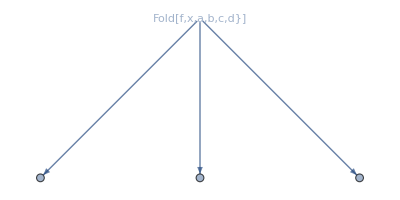

```mathematica
Graph[{"Fold[f,x,a,b,c,d}]",Fold[{f,x,a,b,c,d}],Fold[f,{x,a,b,c,d}],Fold[f,x,{a,b,c,d}]},{"Fold[f,x,a,b,c,d}]"->Fold[{f,x,a,b,c,d}],"Fold[f,x,a,b,c,d}]"->Fold[f,{x,a,b,c,d}],"Fold[f,x,a,b,c,d}]"->Fold[f,x,{a,b,c,d}]},VertexShapeFunction->{"Fold[f,x,a,b,c,d}]"->(Inset[Framed["Fold[f,x,a,b,c,d}]"],#]&)}]
```

```mathematica
VertexShapeFunction->{"Fold[f,x,a,b,c,d}]"->(Inset[Framed["Fold[f,x,a,b,c,d}]"],#]&)}(*check options of Framed*)
```

#### Example for Poster Session

```mathematica
input="Fold[f,x,{a,b,c}]";
dropped=StringDrop[input,{#}]&/@Range[StringLength[input]];
filtered=Select[dropped,Not[messageAnalysis[#]]&];
corrected=syntaxCorrectorWithoutNotation[#,True,20]&/@filtered;
filtocor=Thread[filtered[[#]]->corrected[[#]]]&/@Range[Length[filtered]];
intofil=Thread[input->filtered];
```

```mathematica
Column[input]->Column[filtered]->TableForm[corrected]
```

Column[Fold[f,x,{a,b,c}]]→Foldf,x,{a,b,c}]
Fold[f,x,a,b,c}]
Fold[f,x,{a,b,c]
Fold[f,x,{a,b,c}→F[oldf,x,{a,b,c}] | Fo[ldf,x,{a,b,c}] | Fol[df,x,{a,b,c}] | Fold[f,x,{a,b,c}] | Foldf[,x,{a,b,c}] | 
Fold[{f,x,a,b,c}] | Fold[f{,x,a,b,c}] | Fold[f,{x,a,b,c}] | Fold[f,x{,a,b,c}] | Fold[f,x,{a,b,c}] | Fold[f,x,a{,b,c}]
Fold[f,x,{a,b,}c] | Fold[f,x,{a,b,c}] |  |  |  | 
Fold[f,x,{a,b,c}] |  |  |  |  |

```mathematica
graph=Rasterize[Graph[Flatten@{intofil,filtocor},GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Above],VertexLabelStyle->Directive[FontSize->18,Background->White],ImageSize->600],RasterSize->1000,ImageSize->400]
```

-Graphics-

```mathematica
graph=Rasterize[Graph[Flatten@{intofil,filtocor},GraphLayout->"BalloonEmbedding",VertexLabels->Placed["Name",Above],VertexLabelStyle->Directive[FontSize->17,Background->White],ImageSize->600],RasterSize->1000]
```

-Graphics-

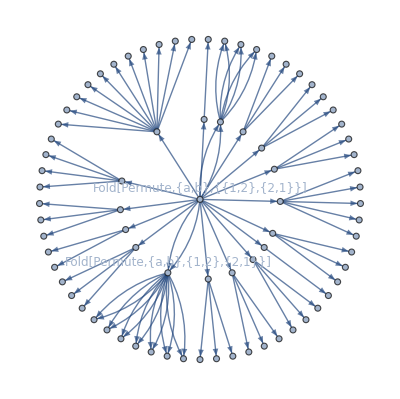

```mathematica
graph=Graph[Flatten@{intofil,filtocor},VertexLabels->{
"Fold[Permute,{a,b},{{1,2},{2,1}}]"->Placed[Style["Fold[Permute,{a,b},{{1,2},{2,1}}]",FontFamily->"Times New Roman",FontSize->12,Background->White],Above],
"Fold[Permute,{a,b},{1,2},{2,1}}]"->Placed[Style["Fold[Permute,{a,b},{1,2},{2,1}}]",FontFamily->"Times New Roman",FontSize->12,Background->White],Above]
},GraphLayout->"RadialEmbedding"]
```

```mathematica
img1=Rasterize[graph,RasterSize->1000]
```

-Graphics-

```mathematica
ImageDimensions[img1]
```

{360,359}

```mathematica
img2=Graphics[{EdgeForm[{Black,Thickness[0.001]}],
Blue,Opacity[0.25],Disk[{180,180},40],
Red,Opacity[0.25],Disk[{180,180},90],
Green,Opacity[0.25],Disk[{180,180},175]
}];
Show[img1,img2]
```

-Graphics-

```mathematica
img2=Graphics[{EdgeForm[{Black,Thickness[0.01]}],Red,Opacity[0.25],Disk[{50,50},10]}];
```

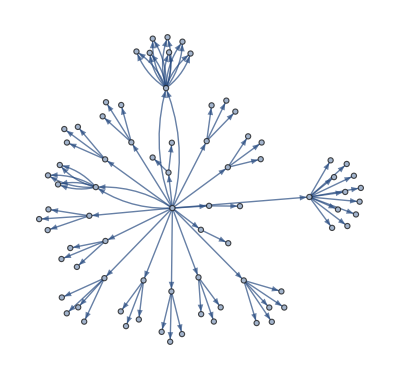

```mathematica
Graph[Flatten@{intofil,filtocor},VertexLabels->Placed["Name",Tooltip]]
```

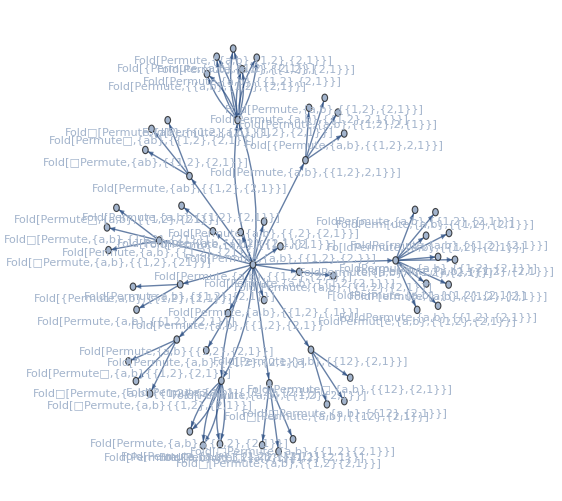

```mathematica
Graph[Flatten@{intofil,filtocor},VertexLabels->Placed["Name",Below]]
```

Data Sources Links/References

Future Directions

1) Complete the neural net.
2) Introduce the new features in algorithm.
3) Improve algorithm by adding a possibility to add in string 2 or more additional characters.

Background Info Links/References

Keywords

Syntax correction

Text analysing

Neural Net

Prediction of sentence

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```